```mathematica
(*The math for this is located in UH One Note/superConductivity/1D domain walls/ High kappa limit in 1D.*)
```

```mathematica
ClearAll["Global`*"]
```

## (*Lower Critical field Calculation*)

```mathematica
DSolve[{g'[x]==-g[x]*Sqrt[1-g[x]^2/2]},g[x],x]
DSolve[{g'[x]==+g[x]*Sqrt[1-g[x]^2/2]},g[x],x]
```

{{g[x]→-√2 √(1-Tanh[x-√2 C[1]]^2)},{g[x]→√2 √(1-Tanh[x-√2 C[1]]^2)}}

{{g[x]→-√2 √(1-Tanh[x+√2 C[1]]^2)},{g[x]→√2 √(1-Tanh[x+√2 C[1]]^2)}}

```mathematica
g1[x_,c_]:=-√2 √(1-Tanh[x-√2 c]^2)
g2[x_,c_]:=√2 √(1-Tanh[x-√2 c]^2)
Ψ1[x_,c_]:=Sqrt[1-g1[x,c]^2]
Ψ2[x_,c_]:=Sqrt[1-g2[x,c]^2]
Manipulate[Plot[{g1[x,c],g2[x,c],Ψ1[x,c],Ψ2[x,c]},{x,-10,10},PlotRange->{-2,2},PlotLegends->{"g1","g2","Ψ1","Ψ2"}],{{c,0},-10,10}]
Manipulate[Plot[{g2[x,c],Ψ2[x,c],Sqrt[-1+2 Tanh[√2 c-x]^2]},{x,-10,10},PlotRange->{-2,2},PlotLegends->{"g2","Ψ2","√(1-g^2)"}],{{c,0},-10,10}]
```

```mathematica
1-g2[x,c]^2//Expand
Manipulate[Plot[{1-g2[x,c]^2,g2[x,c]},{x,-10,10},PlotRange->{-2,2},PlotLegends->{"1-g_2(x)^2","g_2(x)"}],{{c,0},-10,10}]
```

-1+2 Tanh[√2 c-x]^2

1

0.881374

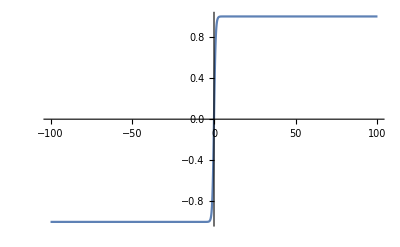

```mathematica
(*Making sure that tanh approaches 1 from below. That way the test function is below 1.*)
Limit[Tanh[x],x->Infinity]
ArcTanh[1/Sqrt[2]]//N
Plot[Tanh[x],{x,-100,100}]
```

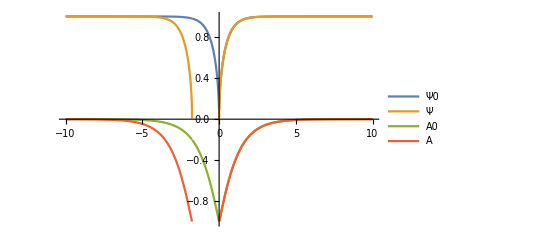

```mathematica
(*Defining a Test function from the solution of the GL eqns.*)
Ψ0[x_]:=Piecewise[{{Sqrt[2*Tanh[x+ArcTanh[1/Sqrt[2]]]^2-1],x>=0},{Sqrt[2*Tanh[x-ArcTanh[1/Sqrt[2]]]^2-1],x<0}}]
Ψ[x_]:=Sqrt[2*Tanh[x+ArcTanh[1/Sqrt[2]]]^2-1]
A0[x_]:=Piecewise[{{-Sqrt[2]*Sqrt[1-Tanh[x+ArcTanh[1/Sqrt[2]]]^2],x>=0},{-Sqrt[2]*Sqrt[1-Tanh[x-ArcTanh[1/Sqrt[2]]]^2],x<0}}](*Sqrt[1-Ψ0[x]^2]*)
A[x_]:=-Sqrt[2]*Sqrt[1-Tanh[x+ArcTanh[1/Sqrt[2]]]^2]
Plot[{Ψ0[x],Ψ[x],A0[x],A[x]},{x,-10,10},PlotRange->{-1,1},PlotLegends->{"Ψ0","Ψ","A0","A"}]
```

```mathematica
(*Evaluating the energy for the corresponding test function*)
Manipulate[Integrate[((1-Ψ[x]^2)^2)/2+Ψ[x]^2*A[x]^2+(D[A[x],x])^2-2*H*D[A[x],x],{x,0,L}],{L,100,1000}]
2*Integrate[((1-Ψ[x]^2)^2)/2+Ψ[x]^2*A[x]^2+(D[A[x],x])^2-2*H*D[A[x],x],{x,0,Infinity}](*Note that the energy is negative if H>=(4-√2)/6*)
(*2/κ^2*NIntegrate[(D[Ψ[x],x])^2,{x,0,5}](*This is non-Integrable. Check section below for how we concluded this.*)*)
2*Integrate[(D[A[x],x])^2-2*H*D[A[x],x],{x,0,Infinity}](*Even though ∂Ψ^2 is not in L^2(0,1), we know that (∂A-H)^2 is in L^2.*)
2*Integrate[((1-Ψ[x]^2)^2)/2+Ψ[x]^2*A[x]^2,{x,0,Infinity}]
```

2/3 (4-√2-6 H)

1/3 (4-√2-12 H)

1/3 (4-√2)

```mathematica
(*Computing numeric approx.*)
(4-√2)/6//N
1/Sqrt[2]//N
```

0.430964

0.707107

```mathematica
(*Testing if the High-kappa soln test function is integrable or not.*)
DPsi[x_]:=D[Ψ[x],x]
DPsi[x]
Asymptotic[DPsi[x]^2,x->0]
Manipulate[NIntegrate[{DPsi[x]^2,1/(2 √2 x)},{x,l,5}],{{l,1},10^-5,1}]
(*The answer is no, cause (∂Ψ)^2~1/x as x->0*)
```

(2 Sech[x+ArcTanh[1/(√2)]]^2 Tanh[x+ArcTanh[1/(√2)]])/(√(-1+2 Tanh[x+ArcTanh[1/(√2)]]^2))

1/(2 √2 x)

```mathematica
(*Checking the energy of the modified Test functions*)
Ψm[x_,ϵ_]:=Piecewise[{{Sqrt[2*Tanh[x+ArcTanh[1/Sqrt[2]]]^2-1],x>=ϵ},{x/ϵ*Sqrt[2*Tanh[ϵ+ArcTanh[1/Sqrt[2]]]^2-1],0<=x<ϵ}}]
Am[x_,ϵ_]:=-Sqrt[2]*Sqrt[1-Tanh[x+ArcTanh[1/Sqrt[2]]]^2]
Manipulate[Plot[{Ψm[x,ϵ],Am[x,ϵ]},{x,0,10}],{ϵ,0,1}](*Plotting the Modified functions.*)
Manipulate[Integrate[((1-(Ψm[x,ϵ])^2)^2)/2+(Ψm[x,ϵ])^2*(Am[x,ϵ])^2+(D[Am[x,ϵ],x])^2-2*H*D[Am[x,ϵ],x],{x,0,Infinity}]//Simplify,{{ϵ,0.1},0,1}](*Checking the Energy without ∂Ψm*)
Manipulate[Integrate[((1-Ψm[x,ϵ]^2)^2)/2+Ψm[x,ϵ]^2*A[x]^2+(D[A[x],x])^2-2*H*D[A[x],x],{x,0,L}]+1/κ^2*Integrate[(D[Ψm[x,ϵ],x])^2,{x,0,L}],{L,100,1000},{{ϵ,0.1},0,1}](*Checking the Total Energy*)
```

```mathematica
(*Continuation of the above, checking each energy separately.*)
Simplify[Integrate[((1-(Ψm[x,ϵ])^2)^2)/2,{x,0,Infinity}],ϵ>0]
Simplify[Integrate[(D[Am[x,ϵ],x])^2-2*H*D[Am[x,ϵ],x],{x,0,Infinity}],ϵ>0]
Simplify[1/κ^2*Integrate[(D[Ψm[x,ϵ],x])^2,{x,0,Infinity}],ϵ>0]
(*Uncomment Below to see the full expression*)
(*Simplify[Integrate[(Ψm[x,ϵ])^2*(Am[x,ϵ])^2,{x,0,Infinity}],ϵ>0]*)
(*Integrate[((1-(Ψm[x,ϵ])^2)^2)/2,{x,0,Infinity},Assumptions->ϵ>0]+Integrate[(Ψm[x,ϵ])^2*(Am[x,ϵ])^2,{x,0,Infinity},Assumptions->ϵ>0]+2/κ^2*Integrate[(D[Ψm[x,ϵ],x])^2,{x,0,Infinity},Assumptions->ϵ>0]*)
```

2/15 (2 (5+ϵ)+ϵ (4+Cosh[2 (ϵ+ArcCoth[√2])]) Sech[ϵ+ArcCoth[√2]]^4-15 Tanh[ϵ+1/2 Log[3+2 √2]]+5 Tanh[ϵ+1/2 Log[3+2 √2]]^3)

1/6 (4-√2-12 H)

-1/(12 ϵ κ^2)(12-4 ϵ+6 √2 ϵ Log[1+√2]+3 √2 ϵ Log[Sinh[ϵ]/((√2 Cosh[ϵ]+Sinh[ϵ]) (1+√2 Tanh[ϵ+ArcTanh[1/(√2)]]))]-24 Tanh[ϵ+ArcTanh[1/(√2)]]^2+4 (ϵ+2 ϵ Sech[ϵ+1/2 Log[3+2 √2]]^2) Tanh[ϵ+1/2 Log[3+2 √2]])

```mathematica
(*Minimizing wrt ϵ (estimating the min). We remove the (A'-H)^2 term since that is independent of ϵ*)
Manipulate[NIntegrate[((1-Ψm[x,ϵ]^2)^2)/2+Ψm[x,ϵ]^2*A[x]^2,{x,0,Infinity}]+1/κ^2*NIntegrate[(D[Ψm[x,ϵ],x])^2,{x,0,Infinity}],{{κ,2},0.001,10},{{ϵ,1.2},0,10}]
```

```mathematica
(*Trying to get a closed form for the trouble some term Subscript[Ψ, ϵ]^2 Subscript[A, ϵ]^2 by simplifying the problem. Doesnt seem to work*)
Integrate[(Ψ[x])^2*(A[x])^2,{x,0,Infinity}](*This is the original unmodifed expression.*)
(*(1/ϵ*Sqrt[2*Tanh[ϵ+ArcTanh[1/Sqrt[2]]]^2-1])^2*Integrate[x^2*A[x]^2,{x,0,ϵ}]*)
(*Simplify[Integrate[(Ψ[x])^2*(A[x])^2,{x,ϵ,Infinity}],ϵ>0]*)
```

2/3 (-1+√2)

```mathematica
(*Estimating the answer based on the numerical approximation of ϵ at κ=2,*)
0.6677227330856448/2+(4-Sqrt[2])/12
```

0.549344

## Upper Critical Field Calculation

```mathematica
(*We are solving the linearized equations.*)
DSolve[{v''[x]==(H^2*x^2-1)*v[x]*κ^2},v[x],x]
{vals,funs}=DEigensystem[{-v''[x]+x^2*v[x]},v[x],{x,-10,10},5];
```

{{v[x]→C[2] ParabolicCylinderD[(-H-κ)/(2 H),ⅈ √2 √H x √κ]+C[1] ParabolicCylinderD[(-H+κ)/(2 H),√2 √H x √κ]}}

Set::shape: Lists {vals,funs} and DEigensystem[{x^2 v[x]-v''[x]},v[x],{x,-10,10},5] are not the same shape.

```mathematica
(*Defining the solutions and checking if it satisfies the ODE*)
v[x_,c1_,c2_,H_,κ_]:=c1*ParabolicCylinderD[(-H+κ)/(2 H),√2 √H x √κ]+c2*ParabolicCylinderD[(-H-κ)/(2 H),ⅈ √2 √H x √κ]
D[v[x,c1,c2,H,κ],{x,2}]-(H^2*κ^2*x^2-κ^2)*v[x,c1,c2,H,κ]//Simplify
```

0

```mathematica
(*Plotting the solution*)
Manipulate[Plot[{Re[v[x,c1,c2,H,κ]],d+Im[v[x,c1,c2,H,κ]]},{x,0,10},PlotLegends->{"Re[v]","Im[v]","Parabolic"}],{{c1,1},-10,10},{{c2,1},-10,10},{H,0.01,10},{{κ,2},0,10},{d,1,1000}](*From this it turns out that v in general in complex valued.*)
Manipulate[Plot[{ParabolicCylinderD[(-H-κ)/(2 H),ⅈ  x],ParabolicCylinderD[(-H+κ)/(2 H),x]},{x,0,10},PlotLegends->{"D_((-H - κ)/(2 H))[i*x]","D_((-H + κ)/(2 H))[x]"}],{H,0.01,10},{{κ,2},0,10}](*The x argument is scaled by x'=√(2*H*κ)*x*)
```

```mathematica
(*IT seems like the parabolic cylinder function isnt always real valued. Need to figure out what causes the real value.*)
```